455

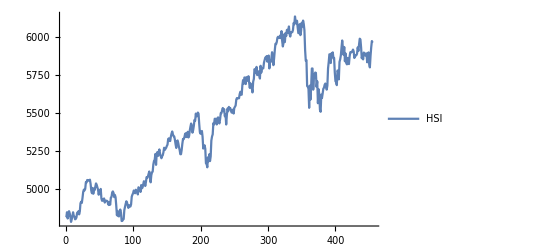

```mathematica
stockData =  FinancialData["^FTSE",{DateObject[{2005,1,1}],DateObject[{2006,10,1}]}];
stockPrices =stockData[[All, 2]];
allRealPrices = stockPrices[[2;;-1]];
allBeforeRealPrices = stockPrices[[1;;-2]];
priceChanges = allRealPrices / allBeforeRealPrices;
Length[stockPrices]
plot = ListLinePlot[{stockPrices},PlotLegends->{"HSI"}]
```

```mathematica
sampleSize=40;
windowSize=1;
methods = {"NearestNeighbors", "NeuralNetwork", "RandomForest", "LinearRegression"}
methods = {"NeuralNetwork"}

predictedPrices = Table[
patterns = Table[priceChanges[[j;;j+windowSize-1]]->priceChanges[[j+windowSize]], {j, i-sampleSize+1,i-windowSize}];
trainingPatterns = patterns[[1;;-2]];
testPatterns = patterns[[-1]];
predictors = Predict[trainingPatterns, Method ->#, PerformanceGoal->"Quality"]&/@  methods;
(*If [i == sampleSize, Print[PredictorInformation[#]] & /@ predictors];*)
#[Keys[testPatterns]]  * allBeforeRealPrices[[i]] & /@  predictors
, {i,sampleSize,Length[priceChanges]}];
realPrices = allRealPrices[[-Length[predictedPrices];;-1]];
beforeRealPrices = allRealPrices[[-Length[predictedPrices]-1;;-2]];
predictedPricesAllMethods = predictedPrices;

AppendTo[methods,"Naive"]
predictedPricesAllMethods = Append[predictedPricesAllMethodsᵀ,beforeRealPrices]ᵀ;
```

{NearestNeighbors,NeuralNetwork,RandomForest,LinearRegression}

{NeuralNetwork}

{NeuralNetwork,Naive}

| MAE | MAPE | Investment profit no fees | Investment profit | Movement accuracy
NeuralNetwork | 21.6838 | 0.425339 | 1.03918 | 0.989455 | 0.487097
Naive | 20.5039 | 0.401734 | 1.10249 | 1.10249 | 0.5

tidilua.tex

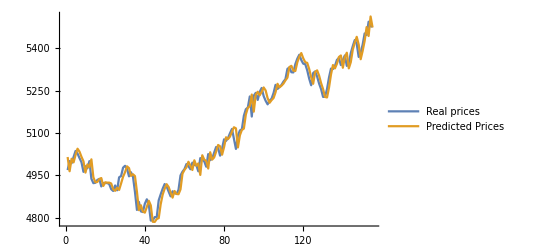

```mathematica
measures = {};
For[i=1, i ≤Length[methods], i++,
predictedPrices = predictedPricesAllMethods[[All,i]];

mae = Total[Abs[ predictedPrices-realPrices]] / Length[realPrices];
mape = Total[Abs[ predictedPrices/realPrices-1]] / Length[realPrices]*100;

movementAccuracy = Total[(Sign[predictedPrices-beforeRealPrices] * Sign[realPrices-beforeRealPrices]+1)/2] / Length[realPrices];

money = 1;
For [t = 2, t ≤Length[predictedPrices], t++,
If [predictedPrices[[t]] ≥realPrices[[t-1]], 
money *= realPrices[[t]] / realPrices[[t-1]];
]
];
moneyNoFees = money;

money = 1;
hasInvested = True;
For [t = 2, t ≤Length[predictedPrices], t++,
transactionFee = money * 0.14 / 100;

If [hasInvested,
If [predictedPrices[[t]] + transactionFee <realPrices[[t-1]],  
money -= transactionFee;
hasInvested=False;
,
money *= realPrices[[t]] / realPrices[[t-1]];
]
,
If [predictedPrices[[t]] - transactionFee ≥realPrices[[t-1]],  
money = (money-transactionFee)*realPrices[[t]] / realPrices[[t-1]];
hasInvested=True;
]
];

]
AppendTo[measures,{mae, mape, moneyNoFees, money, N[movementAccuracy]}]
]


table = TableForm[measures,TableHeadings->{methods, {"MAE", "MAPE", "Investment profit no fees", "Investment profit", "Movement accuracy"}}]
Export["tidilua.tex", table]
ListLinePlot[{realPrices, predictedPricesAllMethods[[All,1]]},PlotLegends->{"Real prices", "Predicted Prices"}]
```

```mathematica
sampleSize = 30;
windowSize =1;
methods = {"NaiveBayes", "LogisticRegression", "NearestNeighbors", "NeuralNetwork", "SupportVectorMachine","RandomForest"};
methods = {"NeuralNetwork"};
priceChanges = allRealPrices;
predictedPrices = ParallelTable[
patterns = Table[priceChanges[[j;;j+windowSize-1]]->Sign[priceChanges[[j+windowSize]]-priceChanges[[j+windowSize-1]]], {j, i-sampleSize+1,i-windowSize}];
trainingPatterns = patterns[[1;;-2]];
testPatterns = patterns[[-1]];
predictors = Classify[trainingPatterns, Method ->#, PerformanceGoal->"TrainingSpeed"]&/@  methods;
(*If [i == sampleSize, Print[ClassifierInformation[#]] & /@ predictors];*)
#[Keys[testPatterns]] & /@  predictors
, {i,sampleSize,Length[priceChanges]}]
realPrices = allRealPrices[[-Length[predictedPrices];;-1]];
beforeRealPrices = allRealPrices[[-Length[predictedPrices]-1;;-2]];
predictedPricesAllMethods = predictedPrices;

AppendTo[methods,"Naive"]
predictedPricesAllMethods = Append[predictedPricesAllMethodsᵀ,beforeRealPrices]ᵀ;
```

{{1},{1},{1},{-1},{1},{-1},{-1},{1},{1},{1},{1},{1},{1},{1},{-1},{-1},{-1},{-1},{1},{1},{1},{1},{-1},{1},{-1},{1},{1},{1},{1},{1},{1},{1},{1},{-1},{-1},{-1},{-1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{-1},{1},{-1},{-1},{-1},{1},{-1},{-1},{1},{1},{1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{1},{-1},{-1},{1},{1},{-1},{1}}

{NeuralNetwork,Naive}

```mathematica
measures = {};
For[i=1, i ≤Length[methods], i++,
predictedPrices = predictedPricesAllMethods[[All,i]];
movementAccuracy = Total[(predictedPrices * Sign[realPrices-beforeRealPrices]+1)/2] / Length[realPrices];
money = 1;
For [t = 2, t ≤Length[predictedPrices], t++,
If [predictedPrices[[t]] > 0,
money *= realPrices[[t]] / realPrices[[t-1]];
]
];
AppendTo[measures,{N[(money-1),3]*100, N[movementAccuracy,3]*100}]
]


table = TableForm[measures,TableHeadings->{methods, {"Investment profit", "Movement accuracy"}}]

ListPlot
```

| Investment profit | Movement accuracy
NeuralNetwork | -2.03112 | 44.9
Naive | -0.610889 | -7064.94

ListPlot

```mathematica
BinomialDistribution[14,0.5]
CDF[BinomialDistribution[5,.6],x]
```

BinomialDistribution[14,0.5]

Piecewise[{{BetaRegularized[0.4,5-Floor[x],1+Floor[x]], 0≤x≤5}, {1, x>5}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{BetaRegularized[0.4,5-Floor[x],1+Floor[x]],0≤x≤5},{1,x>5}},0]]
```

```mathematica
Piecewise[{{0.010240000000000003, 0≤x<1}, {0.08704000000000005, 1≤x<2}, {0.3174400000000001, 2≤x<3}, {0.6630400000000001, 3≤x<4}, {0.9222400000000001, 4≤x<5}, {1, x>5}, {1., x==5}, {0, True}}]

n = 16
Probability[x≥n*0.76,x\[Distributed]BinomialDistribution[n,0.5]] * 100
```

Piecewise[{{0.01024, 0≤x<1}, {0.08704, 1≤x<2}, {0.31744, 2≤x<3}, {0.66304, 3≤x<4}, {0.92224, 4≤x<5}, {1, x>5}, {1., x==5}, {0, True}}]

16

1.06354